```mathematica
size=16;
p=0.58;
pOx=0.5;
initialCells=Table[If[RandomReal[]<p,{1,-1},{0,-1}],{x,1,size},{y,1,size}];
resolution=5;
extended=Table[initialCells[[RoundToBigger[x/resolution]]][[RoundToBigger[y/resolution]]],{x,1,size*resolution},{y,1,size*resolution}];extendedFilled=extended;
extendedFilled=Table[If[extended[[x]][[y]][[1]]==0,0,
If[extended[[x]][[y]][[1]]==1,
If[extended[[x-1]][[y]][[1]]==0||extended[[x+1]][[y]][[1]]==0||extended[[x]][[y-1]][[1]]==0||extended[[x]][[y+1]][[1]]==0,If[Random[]<pOx,0,1],1],1]],
{x,2,size*resolution-1},{y,2,size*resolution-1}];
```

```mathematica
Length[extendedFilled]
```

78

```mathematica
ClusterExtendedFilled=Table[{extendedFilled[[x]][[y]],0},{x,1,size*resolution-2},{y,1,size*resolution-2}]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},76,{{1,0},{1,0},74,{0,0},{0,0}}}
 |  |  |  |

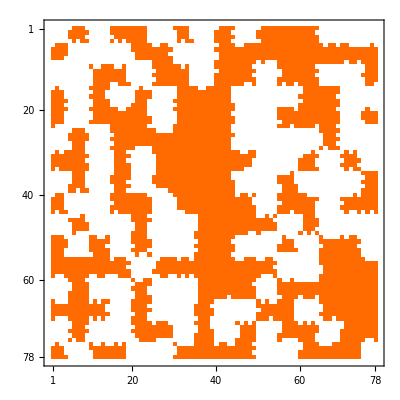

```mathematica
MatrixPlot[Table[ClusterExtendedFilled[[x]][[y]][[1]],{x,1,size*resolution-2},{y,1,size*resolution-2}]]
```

```mathematica
k=1;
Do[If[ClusterExtendedFilled[[x]][[y]][[1]]==1,ClusterExtendedFilled[[x]][[y]][[2]]=k;k++],{x,1,size*resolution-2},{y,1,size*resolution-2}]
```

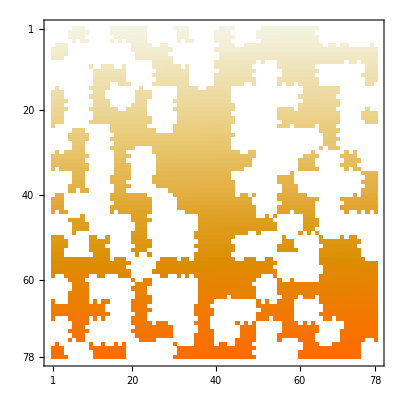

```mathematica
MatrixPlot[Table[ClusterExtendedFilled[[x]][[y]][[2]],{x,1,size*resolution-2},{y,1,size*resolution-2}]]
```

```mathematica
Billy
```

2980

```mathematica
Min[ClusterExtendedFilled[[5]][[5]][[2]]],ClusterExtendedFilled[[3]][[5]][[2]]]
```

```mathematica
Do[Do[
If[ClusterExtendedFilled[[x]][[y]][[1]]==1,
If[ClusterExtendedFilled[[x-1]][[y]][[1]]==1,
Billy=Max[ClusterExtendedFilled[[x]][[y]][[2]],ClusterExtendedFilled[[x-1]][[y]][[2]]];
ClusterExtendedFilled[[x]][[y]][[2]]=Billy;
ClusterExtendedFilled[[x-1]][[y]][[2]]=Billy;
];

If[ClusterExtendedFilled[[x+1]][[y]][[1]]==1,
Billy=Max[ClusterExtendedFilled[[x]][[y]][[2]],ClusterExtendedFilled[[x+1]][[y]][[2]]];
ClusterExtendedFilled[[x]][[y]][[2]]=Billy;
ClusterExtendedFilled[[x+1]][[y]][[2]]=Billy;
];

If[ClusterExtendedFilled[[x]][[y-1]][[1]]==1,
Billy=Max[ClusterExtendedFilled[[x]][[y]][[2]],ClusterExtendedFilled[[x]][[y-1]][[2]]];
ClusterExtendedFilled[[x]][[y]][[2]]=Billy;
ClusterExtendedFilled[[x]][[y-1]][[2]]=Billy;

];

If[ClusterExtendedFilled[[x]][[y+1]][[1]]==1,
Billy=Max[ClusterExtendedFilled[[x]][[y]][[2]],ClusterExtendedFilled[[x]][[y+1]][[2]]];
ClusterExtendedFilled[[x]][[y]][[2]]=Billy;
ClusterExtendedFilled[[x]][[y+1]][[2]]=Billy;
];
],
{x,2,size*resolution-3},{y,2,size*resolution-3}],{ijk,1,33}]
```

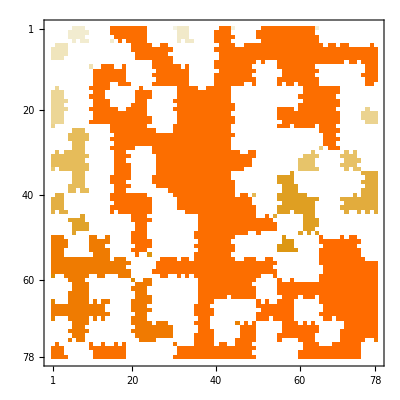

```mathematica
MatrixPlot[Table[ClusterExtendedFilled[[x]][[y]][[2]],{x,1,size*resolution-2},{y,1,size*resolution-2}]]
```

```mathematica
ClusterExtendedFilled[[2]][[7]]
```

{1,37}

```mathematica
Table[ClusterExtendedFilled[[x]][[y]][[2]],{x,1,size*resolution-2},{y,1,size*resolution-2}]
```

```mathematica
CountDistinct[Flatten[Table[ClusterExtendedFilled[[x]][[y]][[2]],{x,1,size*resolution-2},{y,1,size*resolution-2}]]]
```

47